0.94925

```mathematica
1-30000/6000/96//N
```

0.947917

```mathematica
ncells = 30000;
ngenes = 2000;
numis = 288; 
nmice  =10;
(CDF[BinomialDistribution[numis,1-PDF[PoissonDistribution[ncells/ngenes/numis]][0]]][5])^nmice//N
```

7.13914×10^-26

6000

96

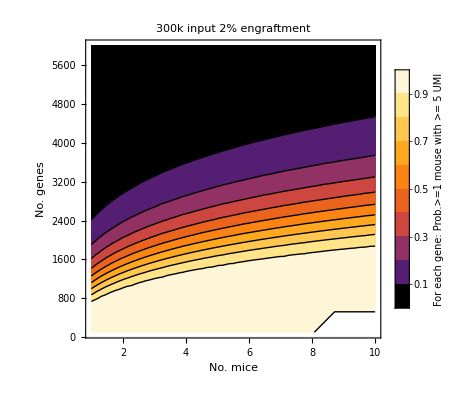

/home/smarkson/Dropbox (HMS)/FITS Paper/Figure 2/B-NoGenesVsNoMicevsProbDetection/GenesVsMiceVsDetectionContoutPlot26Oct2022.pdf

```mathematica
ncells=300000/50
numis=96
plot = ContourPlot[1-(CDF[BinomialDistribution[numis,1-PDF[PoissonDistribution[ncells/ngenes/numis]][0]]][4])^nmice, {nmice,1,10},{ngenes,100,6000},
ClippingStyle->Automatic, PlotLegends-> BarLegend[Automatic, LegendLabel->"For each gene:\nProb.>=1 mouse\nwith >= 5 UMI"],ColorFunction->ColorData["SunsetColors"], PlotTheme->"Scientific", FrameLabel->{"No. mice","No. genes"}, LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20], PlotLabel->"300k input\n2% engraftment"]
Export["/home/smarkson/Dropbox (HMS)/FITS Paper/Figure 2/B-NoGenesVsNoMicevsProbDetection/GenesVsMiceVsDetectionContoutPlot26Oct2022.pdf",plot, ImageResolution->300]
```

6000

96

1000

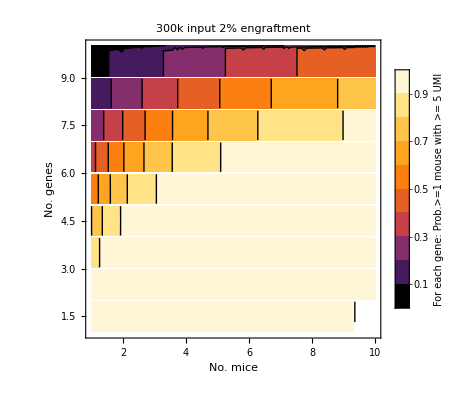

```mathematica
ncells=300000/50 (*accounts for very low engraftment*)
numis=96
ngenes = 1000
plot = ContourPlot[1-(CDF[BinomialDistribution[numis,1-PDF[PoissonDistribution[ncells/ngenes/numis]][0]]][detectedumis])^nmice, {nmice,1,10},{detectedumis,1,10},
ClippingStyle->Automatic, PlotLegends-> BarLegend[Automatic, LegendLabel->"For each gene:\nProb.>=1 mouse\nwith >= 5 UMI"],ColorFunction->ColorData["SunsetColors"], PlotTheme->"Scientific", FrameLabel->{"No. mice","No. genes"}, LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20], PlotLabel->"300k input\n2% engraftment"](*
Export["/home/smarkson/Dropbox (HMS)/FITS Paper/Figure 2/B-NoGenesVsNoMicevsProbDetection/GenesVsMiceVsDetectionContoutPlot26Oct2022.pdf",plot, ImageResolution->300]*)
```

6000

96

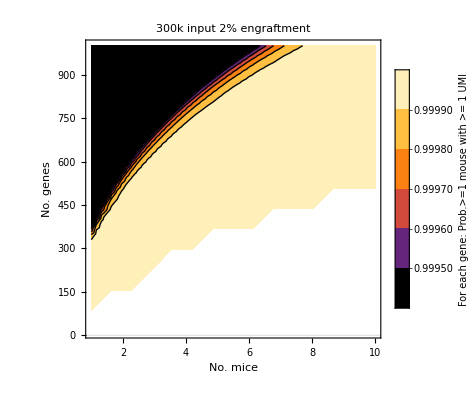

```mathematica
ncells=300000/50
numis=96
plot = ContourPlot[1-(CDF[BinomialDistribution[numis,1-PDF[PoissonDistribution[ncells/ngenes/numis]][0]]][4])^nmice, {nmice,1,10},{ngenes,10,1000},
ClippingStyle->Automatic, PlotLegends-> BarLegend[Automatic, LegendLabel->"For each gene:\nProb.>=1 mouse\nwith >= 1 UMI"],ColorFunction->ColorData["SunsetColors"], PlotTheme->"Scientific", FrameLabel->{"No. mice","No. genes"}, LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20], PlotLabel->"300k input\n2% engraftment"]
```

```mathematica
ncells=300000/50
numis=96
plot = ContourPlot[1-(CDF[BinomialDistribution[numis,1-PDF[PoissonDistribution[ncells/ngenes/numis]][0]]][4])^nmice, {nmice,1,10},{ngenes,100,6000},
ClippingStyle->Automatic, PlotLegends-> BarLegend[Automatic, LegendLabel->"For each gene:\nProb.>=1 mouse\nwith >= 5 UMI"],ColorFunction->ColorData["SunsetColors"], PlotTheme->"Scientific", FrameLabel->{"No. mice","No. genes"}, LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20], PlotLabel->"300k input\n2% engraftment"]
```

6000

96

-Graphics-

```mathematica
PDF[PoissonDistribution[ncells/ngenes/numis]]
```

```mathematica
BinomialDistribution[ngenes, 1-(CDF[BinomialDistribution[numis,1-PDF[PoissonDistribution[ncells/ngenes/numis]][0]]][4])^nmice]
```

1000

General::munfl: Exp[-791.338] is too small to represent as a normalized machine number; precision may be lost.

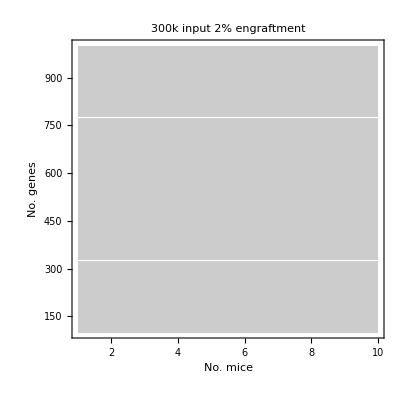

```mathematica
ngenes = 1000
plot = ContourPlot[CDF[BinomialDistribution[ngenes, 1-(CDF[BinomialDistribution[numis,1-PDF[PoissonDistribution[ncells/ngenes/numis]][0]]][4])^nmice]][ngenesdetected], {nmice,1,10},{ngenesdetected,100,1000},
ClippingStyle->Automatic, PlotLegends-> BarLegend[Automatic, LegendLabel->"For each gene:\nProb.>=1 mouse\nwith >= 5 UMI"],ColorFunction->ColorData["SunsetColors"], PlotTheme->"Scientific", FrameLabel->{"No. mice","No. genes"}, LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20], PlotLabel->"300k input\n2% engraftment"]
```

General::munfl: Exp[-5678.09] is too small to represent as a normalized machine number; precision may be lost.

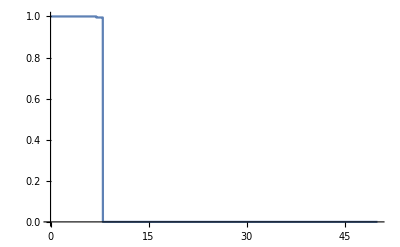

```mathematica
ngenes = 1000;
nmice = 10;
ngenesdetected = 900;
Plot[1-CDF[BinomialDistribution[ngenes, 1-(CDF[BinomialDistribution[numis,1-PDF[PoissonDistribution[ncells/ngenes/numis]][0]]][numisrecovered])^nmice]][ngenesdetected],{numisrecovered,0,50}]
```

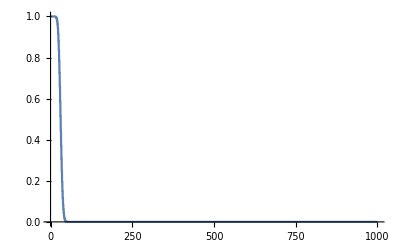
Overlap[{-Graphics-,-Graphics-}]

```mathematica
ngenes = 1000;
nmice = 1;
ngenesdetected = 900;
numisrecovered=10;
p1=Plot[1-CDF[BinomialDistribution[ngenes, 1-(CDF[BinomialDistribution[numis,1-PDF[PoissonDistribution[ncells/ngenes/numis]][0]]][numisrecovered])^nmice]][ngenesdetected],{ngenesdetected,0,1000}];
p2=Plot[{1-CDF[BinomialDistribution[ngenes, 1-(CDF[BinomialDistribution[numis,1-PDF[PoissonDistribution[ncells/ngenes/numis]][0]]][numisrecovered])^nmice]][ngenesdetected]},{ngenesdetected,0,1000}];
Overlap[{p1,p2}]
```

1.-1. (Piecewise[{{BetaRegularized[0.99903^nmice,8000.-1. Floor[ngenesdetected],1.+Floor[ngenesdetected]], 0.≤ngenesdetected<8000.}, {1., ngenesdetected≥8000.}, {0., True}}])

General::munfl: 0.99903^808000 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.99903^1208000 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.99903^1608000 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

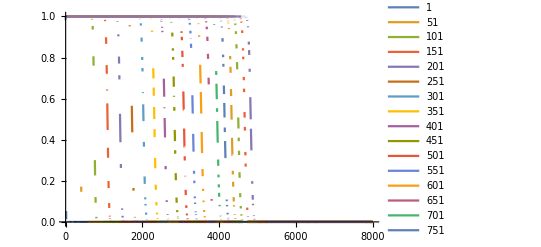

```mathematica
numisrecovered=1;
ngenes = 8000;
numis = 96;
numisrecovered=4;
ncells = 300000/50;
1-CDF[BinomialDistribution[ngenes, 1-(CDF[BinomialDistribution[numis,1-PDF[PoissonDistribution[ncells/ngenes/numis]][0]]][numisrecovered])^nmice]][ngenesdetected]//N
curves = Table[1-CDF[BinomialDistribution[ngenes, 1-(CDF[BinomialDistribution[numis,1-PDF[PoissonDistribution[ncells/ngenes/numis]][0]]][numisrecovered])^nmice]][ngenesdetected],{nmice,1,1000,50}];
Plot[curves, {ngenesdetected,0,ngenes},PlotRange->All,PlotLegends->Table[i,{i,1,1000,50}]]
```

```mathematica
n
```

```mathematica
Clear[ngenesdetected]
```

```mathematica
numis
```

96

```mathematica
ngenes
```

1000

1

```mathematica
numisrecovered=1;
ngenesmax = 20000;
numis = 96;
numisrecovered=4;
curves = Table[1-CDF[BinomialDistribution[ngenes, 1-(CDF[BinomialDistribution[numis,1-PDF[PoissonDistribution[ncells/ngenes/numis]][0]]][numisrecovered])^nmice]][ngenesdetected],{nmice,1,1000,50}];
Plot[curves, {ngenes,0,ngenesmax},PlotRange->All,PlotLegends->Table[i,{i,1,1000,50}]]
```

-Graphics-

```mathematica
nmice=1
ContourPlot[1-CDF[BinomialDistribution[ngenes, 1-(CDF[BinomialDistribution[numis,1-PDF[PoissonDistribution[ncells/ngenes/numis]][0]]][Floor[numisrecovered]])^nmice]][Floor[ngenes*9/10]],{ngenes,100,20000},{numisrecovered, 1,3}]
```

1

BinomialDistribution::nnintprm: Parameter 101.421 at position 1 in BinomialDistribution[101.421,1.] is expected to be a non-negative integer.

General::stop: Further output of BinomialDistribution::nnintprm will be suppressed during this calculation.

-Graphics-

```mathematica
Clear [ngenes]
```

```mathematica
ngenes = 500;
numisrecovered=1;
nmice=1;
Plot[
1-CDF[BinomialDistribution[ngenes, 1-(CDF[BinomialDistribution[numis,1-PDF[PoissonDistribution[ncells/ngenes/numis]][0]]][Floor[numisrecovered]])^nmice]][50],{ngenes, 100,1000}]
```

BinomialDistribution::nnintprm: Parameter 100.018 at position 1 in BinomialDistribution[100.018,1.] is expected to be a non-negative integer.

General::stop: Further output of BinomialDistribution::nnintprm will be suppressed during this calculation.

-Graphics-

```mathematica
probability_of_n_or_more_genes_detected_at_a_given_recovery_threshold(ncells=300000/50,numisrecoveredthreshold=5,numis=96,ngenes=x,ngenesdetected=5,npools=npool)
```

BinomialDistribution::nnintprm: Parameter 100.018 at position 1 in BinomialDistribution[100.018,1.] is expected to be a non-negative integer.

General::stop: Further output of BinomialDistribution::nnintprm will be suppressed during this calculation.

-Graphics-

```mathematica
Floor[ngenes*9/10]
```

450

4

General::munfl: Exp[-2726.66] is too small to represent as a normalized machine number; precision may be lost.

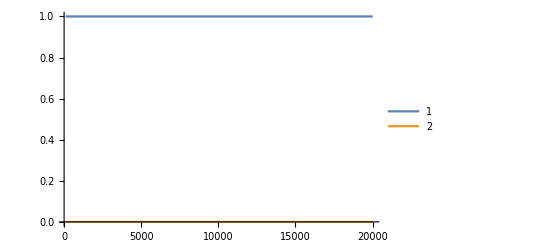

```mathematica
numisrecovered=1;
ngenes = 8000;
numis = 96;
numisrecovered=4;
ngenesdetected=
nmice = 4
curves = Table[1-CDF[BinomialDistribution[ngenes, 1-(CDF[BinomialDistribution[numis,1-PDF[PoissonDistribution[ncells/ngenes/numis]][0]]][numisrecovered])^nmice]][ngenes/2],{numisrecovered,1,2}];
Plot[curves, {ngenes,100,20000},PlotRange->All,PlotLegends->Table[i,{i,1,2}]]
```

```mathematica
1-CDF[BinomialDistribution[ngenes, 1-(CDF[BinomialDistribution[numis,1-PDF[PoissonDistribution[ncells/ngenes/numis]][0]]][Floor[numisrecovered]])^nmice]][50]
```

```mathematica
Clear[nmice]
```

```mathematica
1-(CDF[BinomialDistribution[numis,1-PDF[PoissonDistribution[ncells/ngenes/numis]][0]]][Floor[numisrecovered]])^nmice
```

1-(Piecewise[{{BetaRegularized[ⅇ^(-ncells/(ngenes numis)),numis-Floor[numisrecovered],1+Floor[numisrecovered]], 0≤Floor[numisrecovered]<numis}, {1, Floor[numisrecovered]≥numis}, {0, True}}])^nmice

```mathematica
Clear[numisrecovered]
```

```mathematica
GeneByGeneDetectionRateInAtLeastOneMouse[ncells_,ngenes_,numis_,numisrecoveredthreshold_,nmice_]:=1-BetaRegularized[ⅇ^(-ncells/(ngenes numis)),numis-Floor[numisrecoveredthreshold],1+Floor[numisrecoveredthreshold]]^nmice
```

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

General::stop: Further output of FindRoot::brmp will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,1.05367×10^-8}.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,1.05367×10^-8}.

General::stop: Further output of FindRoot::frmp will be suppressed during this calculation.

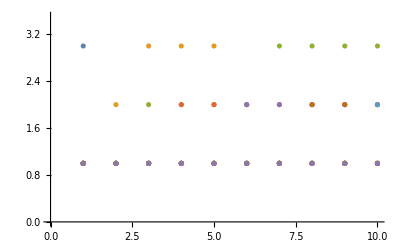

0.664896

```mathematica
ncells=300000/50 ;(*accounts for very low engraftment*)
numis=96;
ngenes=500;
nmice=4;
ListPlot[Table[Table[FindRoot[GeneByGeneDetectionRateInAtLeastOneMouse[ncells,ngenes, numis, numisrecoveredthreshold,nmice]==.9,{numisrecoveredthreshold,1,50}][[1]][[2]],{nmice,1,10}],{ngenes, 1000,20000,1000}]]
```

```mathematica
Solve[GeneByGeneDetectionRateInAtLeastOneMouse[ncells,ngenes, numis, numisrecoveredthreshold,nmice]==9/10,numisrecoveredthreshold]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[1-BetaRegularized[1/ⅇ^(1/8),96-Floor[numisrecoveredthreshold],1+Floor[numisrecoveredthreshold]]^4==9/10,numisrecoveredthreshold]

```mathematica
ncells
```

6000

```mathematica
GeneByGeneDetectionRateInAtLeastOneMouse[ncells,ngenes, numis, numisrecoveredthreshold,1]//N
```

0.935158

```mathematica
Clear[ncells,ngenes,numis,nmice]
```

```mathematica
BetaRegularized[5,1,2]
```

-15

```mathematica
BetaRegularized[.5,3,1]
```

0.125

```mathematica
numis=96
ncells=300000/50
ngenes=1000
numisrecoveredthreshold=2
```

96

6000

1000

2

```mathematica
BetaRegularized[ⅇ^(-ncells/(ngenes numis)),numis-Floor[numisrecoveredthreshold],1+Floor[numisrecoveredthreshold]]//N
```

0.0648416

```mathematica
nmice=1
```

1

```mathematica
FindRoot[GeneByGeneDetectionRateInAtLeastOneMouse[ncells,ngenes, numis, numisrecoveredthreshold,nmice]==.9,{numisrecoveredthreshold,1,5}]
```

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

{numisrecoveredthreshold→3.}

```mathematica
Clear[numisrecoveredthreshold]
```

```mathematica
1-CDF[BinomialDistribution[ngenes, 1-(CDF[BinomialDistribution[numis,1-PDF[PoissonDistribution[ncells/ngenes/numis]][0]]][numisrecovered])^nmice]][ngenesdetected]
```

1-(Piecewise[{{BetaRegularized[(Piecewise[{{BetaRegularized[ⅇ^(-ncells/(ngenes numis)),numis-Floor[numisrecovered],1+Floor[numisrecovered]], 0≤numisrecovered<numis}, {1, numisrecovered≥numis}, {0, True}}])^nmice,ngenes-Floor[ngenesdetected],1+Floor[ngenesdetected]], 0≤ngenesdetected<ngenes}, {1, ngenesdetected≥ngenes}, {0, True}}])

```mathematica
Clear[ngenes, numis, ncells, nmice, ngenesdetected, numisrecovered]
```

```mathematica
BetaRegularized[1]
```

BetaRegularized::argtu: BetaRegularized called with 1 argument; 3 or 4 arguments are expected.

BetaRegularized[1]

```mathematica
ngenes = 5000;
numis=96;
ncells=300000/50;
numisrecovered=5;
nmice=1;
ngenesdetected=5;
1-CDF[BinomialDistribution[ngenes, 1-(CDF[BinomialDistribution[numis,1-PDF[PoissonDistribution[ncells/ngenes/numis]][0]]][numisrecovered])^nmice]][ngenesdetected]//N
```

0.640639

```mathematica
1-CDF[BinomialDistribution[ngenes, 1-(CDF[BinomialDistribution[numis,1-PDF[PoissonDistribution[ncells/ngenes/numis]][0]]][numisrecovered])^nmice]][ngenesdetected]
```

1-(Piecewise[{{BetaRegularized[(Piecewise[{{BetaRegularized[ⅇ^(-ncells/(ngenes numis)),numis-Floor[numisrecovered],1+Floor[numisrecovered]], 0≤numisrecovered<numis}, {1, numisrecovered≥numis}, {0, True}}])^nmice,ngenes-Floor[ngenesdetected],1+Floor[ngenesdetected]], 0≤ngenesdetected<ngenes}, {1, ngenesdetected≥ngenes}, {0, True}}])

```mathematica
BetaRegularized[ⅇ^(-ncells/(ngenes numis)),numis-Floor[numisrecovered],1+Floor[numisrecovered]]//N
```

0.998687

```mathematica
numisrecovered=1;
ngenes = 8000;
numis = 96;
numisrecovered=4;
ngenesdetected=3
nmice=1
ncells = 300000/50;
1-CDF[BinomialDistribution[ngenes, 1-(CDF[BinomialDistribution[numis,1-PDF[PoissonDistribution[ncells/ngenes/numis]][0]]][numisrecovered])^nmice]][ngenesdetected]//N
```

3

1

0.950309

60000

96

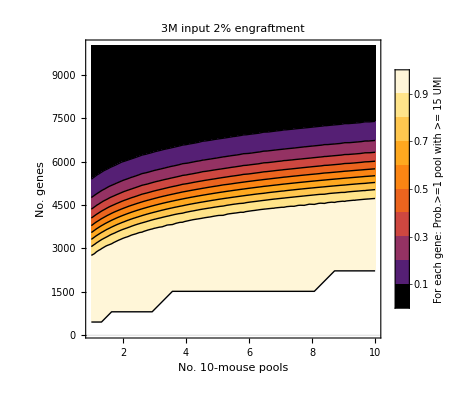

/home/smarkson/Dropbox (HMS)/FITS Paper/Figure 2/B-NoGenesVsNoMicevsProbDetection/GenesVsMiceVsDetectionContoutPlot8Dec2022.pdf

```mathematica
ncells=3000000/50
numis=96
plot = ContourPlot[1-(CDF[BinomialDistribution[numis,1-PDF[PoissonDistribution[ncells/ngenes/numis]][0]]][14])^nmice, {nmice,1,10},{ngenes,100,10000},
ClippingStyle->Automatic, PlotLegends-> BarLegend[Automatic, LegendLabel->"For each gene:\nProb.>=1 pool\nwith >= 15 UMI"],ColorFunction->ColorData["SunsetColors"], PlotTheme->"Scientific", FrameLabel->{"No. 10-mouse pools","No. genes"}, LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20], PlotLabel->"3M input\n2% engraftment"]
Export["/home/smarkson/Dropbox (HMS)/FITS Paper/Figure 2/B-NoGenesVsNoMicevsProbDetection/GenesVsMiceVsDetectionContoutPlot8Dec2022.pdf",plot, ImageResolution->300]
```

6000

96

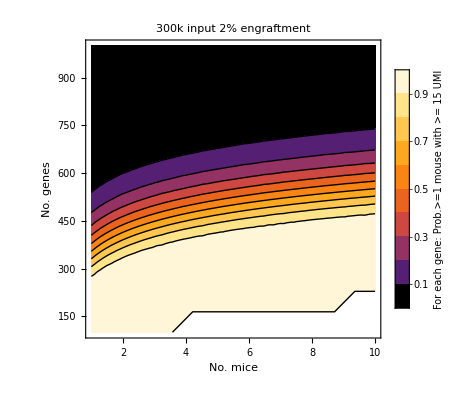

/home/smarkson/Dropbox (HMS)/FITS Paper/Figure 2/B-NoGenesVsNoMicevsProbDetection/GenesVsMiceVsDetectionContoutPlotMouseBasis8Dec2022.pdf

```mathematica
ncells=300000/50
numis=96
plot = ContourPlot[1-(CDF[BinomialDistribution[numis,1-PDF[PoissonDistribution[ncells/ngenes/numis]][0]]][14])^nmice, {nmice,1,10},{ngenes,100,1000},
ClippingStyle->Automatic, PlotLegends-> BarLegend[Automatic, LegendLabel->"For each gene:\nProb.>=1 mouse\nwith >= 15 UMI"],ColorFunction->ColorData["SunsetColors"], PlotTheme->"Scientific", FrameLabel->{"No. mice","No. genes"}, LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20], PlotLabel->"300k input\n2% engraftment"]
Export["/home/smarkson/Dropbox (HMS)/FITS Paper/Figure 2/B-NoGenesVsNoMicevsProbDetection/GenesVsMiceVsDetectionContoutPlotMouseBasis8Dec2022.pdf",plot, ImageResolution->300]
```

6000

96

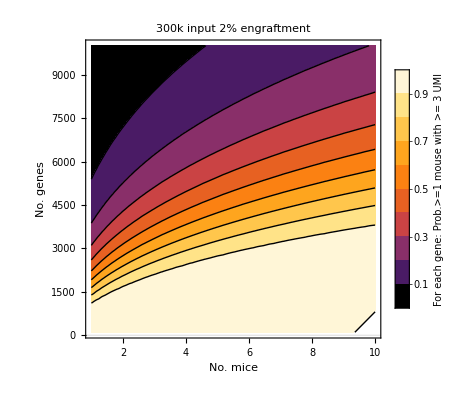

/home/smarkson/Dropbox (HMS)/FITS Paper/Figure 2/B-NoGenesVsNoMicevsProbDetection/GenesVsMiceVsDetectionContoutPlotMouseBasisThreeUMI8Dec2022.pdf

```mathematica
ncells=300000/50
numis=96
plot = ContourPlot[1-(CDF[BinomialDistribution[numis,1-PDF[PoissonDistribution[ncells/ngenes/numis]][0]]][2])^nmice, {nmice,1,10},{ngenes,100,10000},
ClippingStyle->Automatic, PlotLegends-> BarLegend[Automatic, LegendLabel->"For each gene:\nProb.>=1 mouse\nwith >= 3 UMI"],ColorFunction->ColorData["SunsetColors"], PlotTheme->"Scientific", FrameLabel->{"No. mice","No. genes"}, LabelStyle->Directive[FontFamilFlorence Airport,Peretolay->"Arial",Black,FontSize->20], PlotLabel->"300k input\n2% engraftment"]
Export["/home/smarkson/Dropbox (HMS)/FITS Paper/Figure 2/B-NoGenesVsNoMicevsProbDetection/GenesVsMiceVsDetectionContoutPlotMouseBasisThreeUMI8Dec2022.pdf",plot, ImageResolution->300]
```

120

96

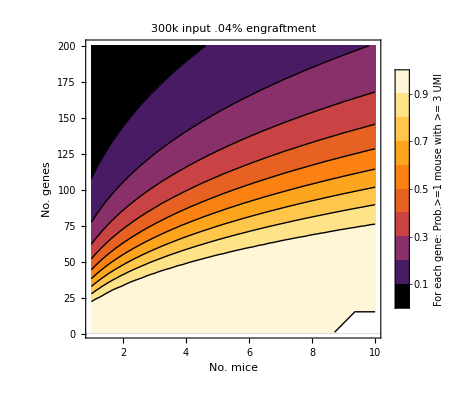

/home/smarkson/Dropbox (HMS)/FITS Paper/Figure 2/B-NoGenesVsNoMicevsProbDetection/GenesVsMiceVsDetectionContoutPlotMouseBasisP04EngraftmentThreeUMI8Dec2022.pdf

```mathematica
ncells=300000/50/50
numis=96
plot = ContourPlot[1-(CDF[BinomialDistribution[numis,1-PDF[PoissonDistribution[ncells/ngenes/numis]][0]]][2])^nmice, {nmice,1,10},{ngenes,1,200},
ClippingStyle->Automatic, PlotLegends-> BarLegend[Automatic, LegendLabel->"For each gene:\nProb.>=1 mouse\nwith >= 3 UMI"],ColorFunction->ColorData["SunsetColors"], PlotTheme->"Scientific", FrameLabel->{"No. mice","No. genes"}, LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20], PlotLabel->"300k input\n.04% engraftment"]
Export["/home/smarkson/Dropbox (HMS)/FITS Paper/Figure 2/B-NoGenesVsNoMicevsProbDetection/GenesVsMiceVsDetectionContoutPlotMouseBasisP04EngraftmentThreeUMI8Dec2022.pdf",plot, ImageResolution->300]
```

120

96

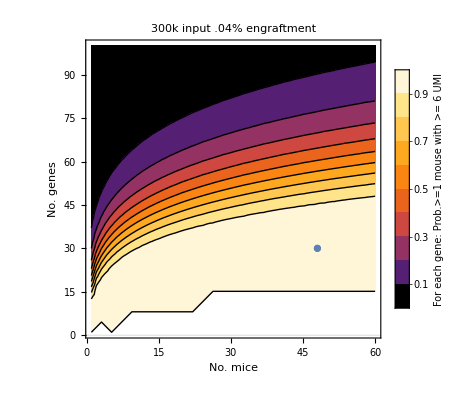

```mathematica
ncells=300000/50/50
numis=96
plot = ContourPlot[1-(CDF[BinomialDistribution[numis,1-PDF[PoissonDistribution[ncells/ngenes/numis]][0]]][5])^nmice, {nmice,1,60},{ngenes,1,100},
ClippingStyle->Automatic, PlotLegends-> BarLegend[Automatic, LegendLabel->"For each gene:\nProb.>=1 mouse\nwith >= 6 UMI"],ColorFunction->ColorData["SunsetColors"], PlotTheme->"Scientific", FrameLabel->{"No. mice","No. genes"}, LabelStyle->Directive[FontFamily->"Arial",Black,FontSize->20], PlotLabel->"300k input\n.04% engraftment"];
plot2 = ListPlot[{{48,30}}];
Show[{plot,plot2}]
(*Export["/home/smarkson/Dropbox (HMS)/FITS Paper/Figure 2/B-NoGenesVsNoMicevsProbDetection/GenesVsMiceVsDetectionContoutPlotMouseBasisP04EngraftmentThreeUMI8Dec2022.pdf",plot, ImageResolution->300]*)
```